The principle used in the Isograph is to substitute r e^(i theta) for z in the polynomial p(z) and then to plot p(z) as a function of theta for a given r in the complex plane. By varying r so that the curve touches the point (0, 0) it is possible to determines a value for one root of the polynomial.

```mathematica
IsoGraphSimulator[eqn_Equal, var_] :=
Module[{p},
Show[GraphicsGrid[Append[Partition[#, 3],
Complement[#, Flatten[Partition[#, 3]]]]& @
(ParametricPlot[Evaluate[{Re[#], Im[#]}&[ 
    (Subtract @@ eqn) /. var -> # Exp[I p]]],{p, 0, 2Pi},
    AspectRatio -> Automatic, Axes -> True, 
    Frame -> True, AxesOrigin -> {0, 0},
    PlotLabel -> ("|" <> ToString[var] <> "|=" <> ToString[N[#, 3]]),
    DisplayFunction -> Identity]& /@ 
        Sort[(x /. NSolve[eqn,var]), Abs[#1] < Abs[#2]&])]]]
```

Here as an example is our quintic r:

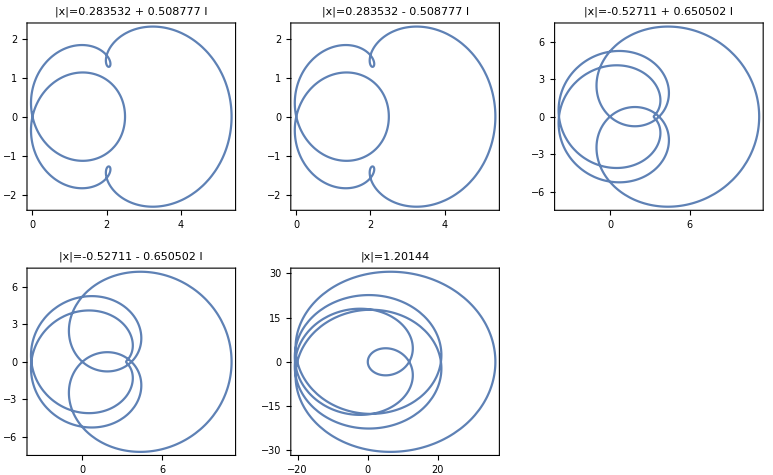

```mathematica
IsoGraphSimulator[ 2 - 2x + 4x^2 + x^3 + 5x^4 - 7x^5 == 0, x]
```